```mathematica
DataOverall=Import["/home/stshammi/Desktop/temp/overall_post.csv","CSV"] (*Ligo Overall Posterior containing spin1,spin2,distance,theta_inclination,gps time, mass1,right-ascension,mass2,declination respectively.*)
```

{{0.170561,0.46512,507.312,2.72953,1.12626×10^9,35.3657,2.18832,33.859,-1.25095},46846,{0.140511,0.815521,324.86,2.64117,1.12626×10^9,42.3546,1.29158,28.7467,-1.23}}
 |  |  |  |

```mathematica
Data1000=RandomChoice[DataOverall,1000]  (*Selected 1000 random data from overall posterior*)
```

{{0.147025,0.290444,257.231,2.14963,1.12626×10^9,43.0279,1.15747,29.1445,-1.15585},998,{0.239793,0.600577,404.288,2.66877,1.12626×10^9,36.0128,1.36239,32.5038,-1.22558}}
 |  |  |  |

```mathematica
A=Mean[DataOverall]
```

{0.350359,0.486834,418.042,2.49079,1.12626×10^9,39.5979,1.89253,31.5798,-1.15253}

```mathematica
B=Mean[Data1000]
```

{0.343294,0.503053,420.466,2.50665,1.12626×10^9,39.7077,1.87778,31.5229,-1.156}

```mathematica
100*Abs[(A-B)]/Abs[B](*Percent Difference between the means of overall posterior and random 1000 data*)
```

{2.05796,3.22425,0.576358,0.633053,2.87899×10^-12,0.276438,0.785849,0.180506,0.300743}

```mathematica
StandardDeviation[DataOverall]
```

{0.22789,0.290591,99.5402,0.507142,0.00340819,2.93588,0.559782,2.77302,0.197342}

```mathematica
StandardDeviation[Data1000]
```

{0.215528,0.290646,99.6444,0.493869,0.0034302,2.96705,0.564064,2.87854,0.180839}

```mathematica
M1Overall=DataOverall[[All,6]] (*Extract mass1 from the overall dataset*)
```

{35.3657,38.9919,41.1164,38.8246,36.0867,35.3432,39.7979,41.1266,40.8909,38.5472,42.4385,39.5321,42.7289,46822,41.165,41.5721,37.9489,43.7925,35.0738,38.3524,36.3972,41.4669,40.9992,36.747,41.4376,39.6713,42.3546}
 |  |  |  |

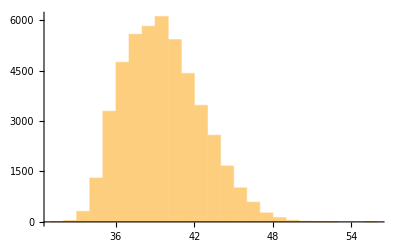

```mathematica
Histogram[M1Overall]
```

```mathematica
M11000=Data1000[[All,6]]; (*Extract mass1 from the Random 1000 data*)
```

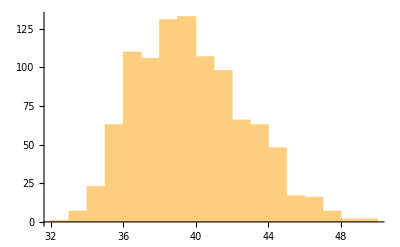

```mathematica
Histogram[M11000]
```

```mathematica
Spin1Overall=DataOverall[[All,1]]
```

{0.170561,0.516418,0.229362,0.496396,0.383741,0.609992,0.423402,0.209471,0.605312,0.393018,0.610475,0.555426,46824,0.576469,0.070841,0.449389,0.148862,0.218133,0.31838,0.667879,0.228978,0.210721,0.00296471,0.514626,0.140511}
 |  |  |  |

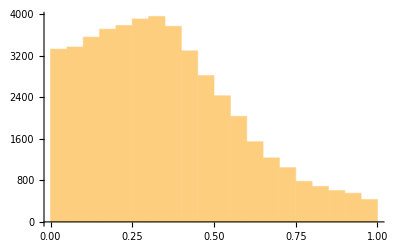

```mathematica
Histogram[Spin1Overall]
```

```mathematica
Spin11000=Data1000[[All,1]];
```

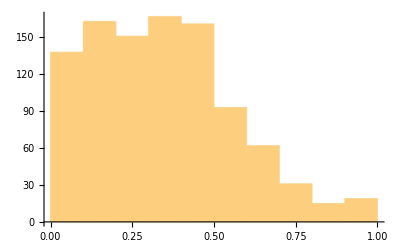

```mathematica
Histogram[Spin11000]
```

```mathematica
Spin2Overall=DataOverall[[All,2]]
```

{0.46512,0.477871,0.812524,0.784072,0.577379,0.959002,0.449435,0.834464,0.890845,0.335276,0.908262,0.963614,46824,0.205723,0.780242,0.236437,0.224012,0.378596,0.0186822,0.352785,0.422516,0.0397549,0.496657,0.893819,0.815521}
 |  |  |  |

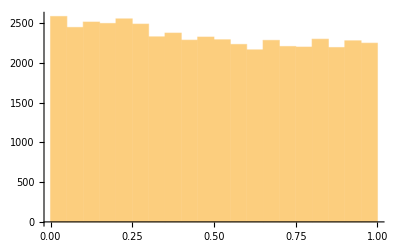

```mathematica
Histogram[Spin2Overall]
```

```mathematica
Spin21000=Data1000[[All,2]];
```

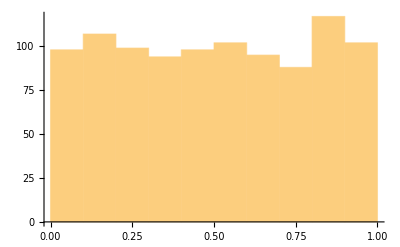

```mathematica
Histogram[Spin21000]
```

```mathematica
A=Data1000[[All,1]]+Data1000[[All,1]];
```

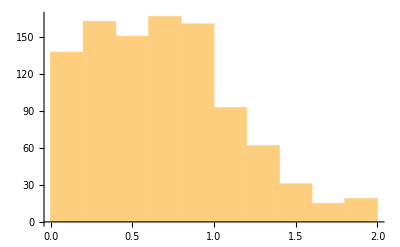

```mathematica
Histogram[A]
```

```mathematica
δMOverall=(DataOverall[[All,6]]-DataOverall[[All,8]])/(DataOverall[[All,6]]+DataOverall[[All,8]])
```

{0.0217656,0.0525423,0.198627,0.0965162,0.0199388,0.0304878,0.0767868,0.197328,0.125634,0.0421099,0.159577,46826,0.0990456,0.280265,0.00777825,0.131734,0.0505731,0.184593,0.108291,0.0352269,0.161333,0.170913,0.191389}
 |  |  |  |

```mathematica
EffSpinOverall=((1+δMOverall)*DataOverall[[All,1]])/2+((1-δMOverall)*(-DataOverall[[All,2]]))/2
```

{-0.140362,0.0453946,-0.188108,-0.0820449,-0.0872375,-0.150587,0.0204942,-0.209498,-0.0487819,0.0442051,46828,0.202583,-0.0361248,-0.0409267,0.158372,0.251751,-0.0614936,0.089895,-0.206543,-0.0692355,-0.246018}
 |  |  |  |

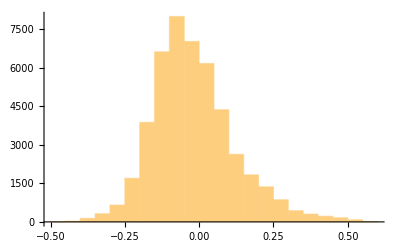

```mathematica
Histogram[EffSpinOverall]
```

```mathematica
Mean[EffSpinOverall]
```

-0.0183438

```mathematica
StandardDeviation[EffSpinOverall]
```

0.138265

```mathematica
δM1000=(Data1000[[All,6]]-Data1000[[All,8]])/(Data1000[[All,6]]+Data1000[[All,8]]);
```

```mathematica
EffSpin1000=((1+δM1000)*Data1000[[All,1]])/2+((1-δM1000)*(-Data1000[[All,2]]))/2;
```

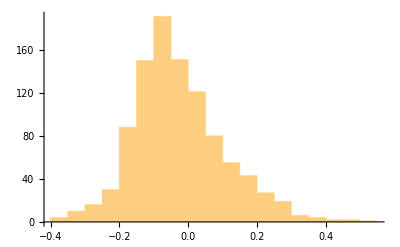

```mathematica
Histogram[EffSpin1000]
```

```mathematica
Mean[EffSpin1000]
```

-0.0275029

```mathematica
StandardDeviation[EffSpin1000]
```

0.132301